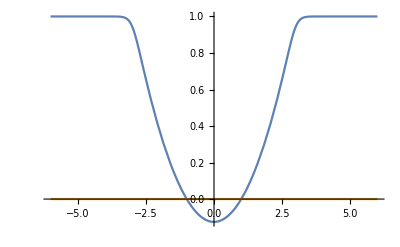

```mathematica
(*Plazma configuration*)
X=3;(*plasma boundary*)
α=0.000000001;(*dissipation, α=ν/ω, ω->ω(1+ⅈα)*)
U=0;(*anizatropy: p^2=4πe^2*n/m, b=eB/(mc), v=p^2/ω^2, u=b^2/ω^2, and with dissipation: v->v(1-ⅈα), u->U(1-ⅈα)*)
Δ=0.05;(*smoothing width, in parts of plasma whight*)

n=1/Δ; smoothingFunc=Function[x,(1-(x/X)^(2n))^-1]; v=Function[x,((X^2-x^2)/(X^2-1))*smoothingFunc[x]*(1-ⅈ*α)]; u=U(1-ⅈ*α);
Eps=({{1-v[x]/(1-u), ⅈ(√u)/(1-u)v[x], 0}, {-ⅈ(√u)/(1-u)v[x], 1-v[x]/(1-u), 0}, {0, 0, 1-v[x]}});
Plot[{Re[Eps[[3,3]]],Im[Eps[[3,3]]]},{x,-2X,2X}]
```

```mathematica
(*Wave configuration*)
χ=20;(*dimensionless wave vector magnitude; χ=Subscript[k, 0] L, and L=1*) 
θ=0.15;(*angel between wave vector and XOZ*)
β=π/2;(*angle between wave vector and magnetic field direction*)
A=1;(*wave magnitude*)
P=({{0}, {1}})ᵀ[[1]];(*wave polarisation*)
k=χ({{Cos[θ]Sin[β]}, {Sin[θ]}, {Cos[θ]Cos[β]}})ᵀ[[1]](*wave vector*)
Ε=A/Norm[P]({{Cos[β], -Sin[θ]Sin[β]}, {0, Cos[θ]}, {-Sin[β], -Sin[θ]Cos[β]}}).P (*Electric field (!!!ESCAPE_SEQUENCE!!!)*)
Β=(k×Ε)/χ(*Magnetic field (!!!ESCAPE_SEQUENCE!!!)*)
```

{19.7754,2.98876,0.}

{-0.149438,0.988771,0.}

{0.,0.,1.}

```mathematica
(*Maxwell equations*)
GeneralSystem = {
(*Ex[x]*Eps[x][[1,1]]+Ey[x]*Eps[x][[1,2]]==kz*By[x]-ky*Bz[x], Bx[x]==ky*Ez[x]-kz*Ey[x],*)
Ey'[x]==ⅈ*χ*(ky*(kz*By[x]-ky*Bz[x]-Ey[x]*Eps[[1,2]])/Eps[[1,1]]+Bz[x]),(*Ey'[x]==ⅈ*χ*(ky*Ex[x]+Bz[x])*)
Ez'[x]==ⅈ*χ*(kz*(kz*By[x]-ky*Bz[x]-Ey[x]*Eps[[1,2]])/Eps[[1,1]]-By[x]),(*Ez'[x]==ⅈ*χ*(kz*Ex[x]-By[x])*)
By'[x]==ⅈ*χ*(ky*(ky*Ez[x]-kz*Ey[x])-Eps[[3,3]]*Ez[x]),(*By'[x]==ⅈ*χ*(ky*Bx[x]-Eps[x][[3,3]]*Ez[x])*)
Bz'[x]==ⅈ*χ*(kz*(ky*Ez[x]-kz*Ey[x])+Eps[[2,1]]*(kz*By[x]-ky*Bz[x]-Ey[x]*Eps[[1,2]])/Eps[[1,1]]+Eps[[2,2]]*Ey[x])(*Bz'[x]==ⅈ*χ*(kz*Bx[x]+Eps[x][[2,1]]*Ex[x]+Eps[x][[2,2]]*Ey[x])*)
}/.{kx->k[[1]]/χ,ky->k[[2]]/χ,kz->k[[3]]/χ};

GeneralInitials = {Ey[2X]==Ε[[2]],Ez[2X]==Ε[[3]],By[2X]==Β[[2]],Bz[2X]==Β[[3]]};
Sol=NDSolveValue[{GeneralSystem,GeneralInitials},{Ey,Ez,By,Bz},{x,-2X,2X}];
```

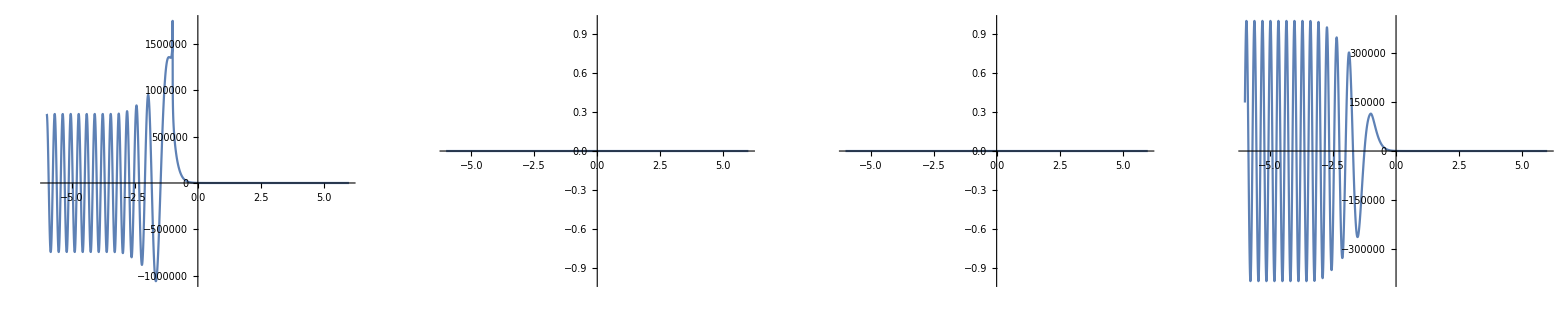

```mathematica
GraphicsRow[Table[Plot[Re[Sol[[i]][x]],{x,-2X,2X},PlotRange->Full],{i,1,4}],ImageSize->{Full,Full} ]
```

```mathematica
(*Polarisation rotations*)
If[P[[1]]==0,Conjugate[P[[2]]]/Abs[P[[2]]],Conjugate[P[[1]]]/Abs[P[[1]]]]({{P[[1]]/Norm[P]}, {P[[2]]/Norm[P]}})ᵀ[[1]](*Transmitted wave*)
(({{Cos[β], 0, -Sin[β]}, {-Sin[β]Sin[θ], Cos[θ], -Cos[β]Sin[θ]}}).({{(kz*By[x]-ky*Bz[x]-Ey[x]*Eps[[1,2]])/Eps[[1,1]]}, {Ey[x]}, {Ez[x]}}))ᵀ[[1]]/.{kx->k[[1]]/χ,ky->k[[2]]/χ,kz->k[[3]]/χ,Ey[x]->Sol[[1]][x],Ez[x]->Sol[[2]][x],By[x]->Sol[[3]][x],Bz[x]->Sol[[4]][x]};
({{a/.NSolve[{a*Exp[ⅈ*k[[1]](-2X)]+b*Exp[-ⅈ*k[[1]](-2X)]==%[[1]]/.x->(-2X),ⅈ*k[[1]]a*Exp[ⅈ*k[[1]](-2X)]-ⅈ*k[[1]]b*Exp[-ⅈ*k[[1]](-2X)]==D[%[[1]],x]/.x->(-2X)},{a,b}][[1]]}, {a/.NSolve[{a*Exp[ⅈ*k[[1]](-2X)]+b*Exp[-ⅈ*k[[1]](-2X)]==%[[2]]/.x->(-2X),ⅈ*k[[1]]a*Exp[ⅈ*k[[1]](-2X)]-ⅈ*k[[1]]b*Exp[-ⅈ*k[[1]](-2X)]==D[%[[2]],x]/.x->(-2X)},{a,b}][[1]]}})ᵀ[[1]];
If[%[[1]]==0,Conjugate[%[[2]]]/Abs[%[[2]]],Conjugate[%[[1]]]/Abs[%[[1]]]]({{(%[[1]])/Norm[%]}, {(%[[2]])/Norm[%]}})ᵀ[[1]](*Initial wave*)
(({{Cos[π-β], 0, -Sin[π-β]}, {-Sin[π-β]Sin[-θ], Cos[-θ], -Cos[π-β]Sin[-θ]}}).({{(kz*By[x]-ky*Bz[x]-Ey[x]*Eps[[1,2]])/Eps[[1,1]]}, {Ey[x]}, {Ez[x]}}))ᵀ[[1]]/.{kx->k[[1]]/χ,ky->k[[2]]/χ,kz->k[[3]]/χ,Ey[x]->Sol[[1]][x],Ez[x]->Sol[[2]][x],By[x]->Sol[[3]][x],Bz[x]->Sol[[4]][x]};
({{b/.NSolve[{a*Exp[ⅈ*k[[1]](-2X)]+b*Exp[-ⅈ*k[[1]](-2X)]==%[[1]]/.x->(-2X),ⅈ*k[[1]]a*Exp[ⅈ*k[[1]](-2X)]-ⅈ*k[[1]]b*Exp[-ⅈ*k[[1]](-2X)]==D[%[[1]],x]/.x->(-2X)},{a,b}][[1]]}, {b/.NSolve[{a*Exp[ⅈ*k[[1]](-2X)]+b*Exp[-ⅈ*k[[1]](-2X)]==%[[2]]/.x->(-2X),ⅈ*k[[1]]a*Exp[ⅈ*k[[1]](-2X)]-ⅈ*k[[1]]b*Exp[-ⅈ*k[[1]](-2X)]==D[%[[2]],x]/.x->(-2X)},{a,b}][[1]]}})ᵀ[[1]];
If[%[[1]]==0,Conjugate[%[[2]]]/Abs[%[[2]]],Conjugate[%[[1]]]/Abs[%[[1]]]]({{(%[[1]])/Norm[%]}, {(%[[2]])/Norm[%]}})ᵀ[[1]](*Reflected wave*)
1-Norm[%%]/Norm[%%%%%](*Dissipation*)
```

{0,1}

{0.+0. ⅈ,1.+0. ⅈ}

{0.+0. ⅈ,1.+0. ⅈ}

0.265107